Data Import

```mathematica
data=Import["/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/howfar_data_with_no_normalization.csv",HeaderLines-> 1];
subjectID=data[[All,1]];
fbGenuine=data[[All,2]];
rcGenuine=data[[All,3]];
imposterID=data[[All,4]];
fbImposter=data[[All,5]];
rcImposter=data[[All,6]];
```

Histogram of the genuine and imposter distributions when measuring the distance between the fa and the fb images.

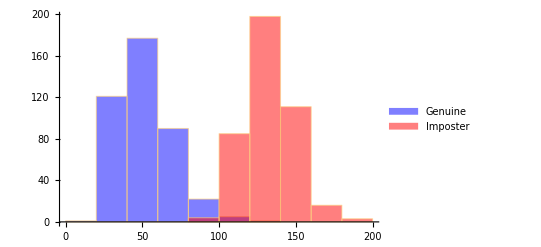

```mathematica
Histogram[{fbGenuine,fbImposter},ChartStyle->{Blue,Red},ChartLegends->{"Genuine", "Imposter"}]
```

Histogram of the genuine and imposter distributions when measuring the distance between the fa and the rc images.

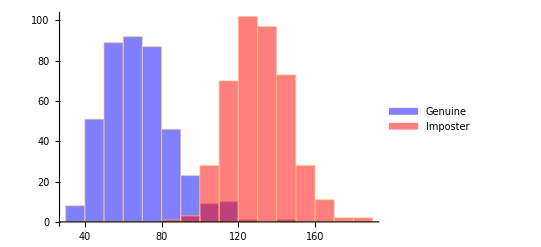

```mathematica
Histogram[{rcGenuine,rcImposter},ChartStyle->{Blue,Red},ChartLegends->{"Genuine", "Imposter"}]
```

Histogram of the genuine and imposter distributions when measuring the distance between the fa and the fb and the rc images.

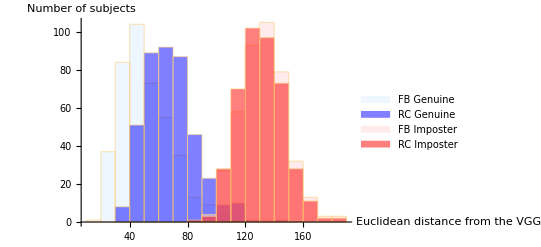

```mathematica
Histogram[{fbGenuine,rcGenuine,fbImposter,rcImposter},ChartStyle->{LightBlue,Blue,LightRed,Red},ChartLegends->{"FB Genuine","RC Genuine","FB Imposter" ,"RC Imposter"}, AxesLabel->{"Euclidean distance from the VGG output for the fa image", "Number of subjects"}]
```

Histogram of the genuine distributions when measuring the distance between the fa and the fb and the rc images.

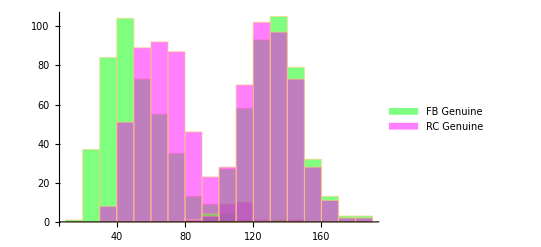

```mathematica
Histogram[{fbGenuine,rcGenuine,fbImposter,rcImposter},ChartStyle->{Green,Magenta},ChartLegends->{"FB Genuine","RC Genuine"}]
```

List plot of the genuine distributions when measuring the distance between the fa and the fb and the rc images.

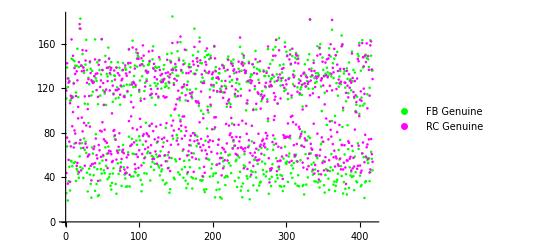

```mathematica
ListPlot[{fbGenuine,rcGenuine,fbImposter,rcImposter},PlotStyle->{Green,Magenta},PlotLegends->{"FB Genuine","RC Genuine"}]
```

List Plot of the genuine and imposter distributions when measuring the distance between the fa and the fb and the rc images.

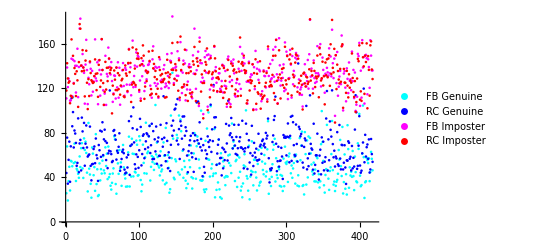

```mathematica
ListPlot[{fbGenuine,rcGenuine,fbImposter,rcImposter},PlotStyle->{Cyan,Blue,Magenta,Red},PlotLegends->{"FB Genuine","RC Genuine","FB Imposter" ,"RC Imposter"}]
```

List Plot of the distances between the fa and the fb and the fa and the rc images for genuines and for imposters. The x axis represents the Euclidean distance between the fa image and the specified other type of image. The y axis is the index of the distance in the input array and does not impact the distributions (essentially, this is a “histogram of dots”).
Another way to say this is  that if you look at a particular y value and draw a horizontal line, the Euclidean distance between that subject’s fa and all its other images will lie on that horizontal line, with their x coordinates determined by the value of that distance.

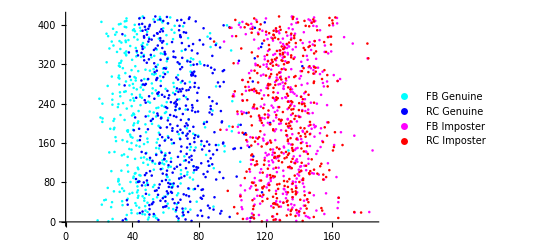

```mathematica
rotateData[d_]:=Table[{d[[i]],i},{i,1,Length[data]}];
ListPlot[rotateData/@{fbGenuine,rcGenuine,fbImposter,rcImposter},PlotStyle->{Cyan,Blue,Magenta,Red},PlotLegends->{"FB Genuine","RC Genuine","FB Imposter" ,"RC Imposter"},AxesOrigin->{0,0}]
```